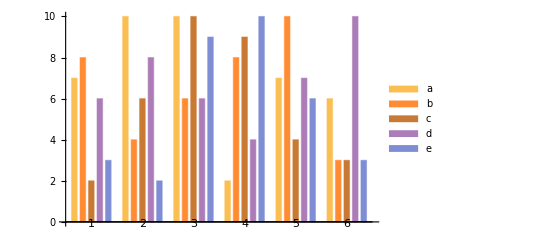

```mathematica
data=RandomInteger[{1,10},{6,5}];
BarChart[data,
ChartLabels->{{"1","2","3","4","5","6"},None},
ChartLegends->{"a","b","c","d","e"}]
```

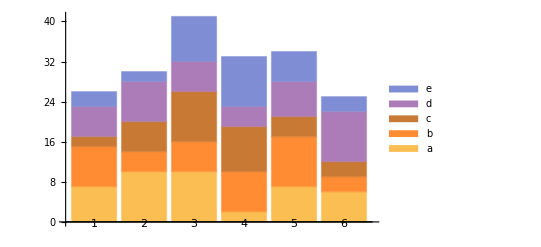

```mathematica
BarChart[data,ChartLayout->"Stacked",ChartLabels->{{"1","2","3","4","5","6"},None},
ChartLegends->{"a","b","c","d","e"}]
```

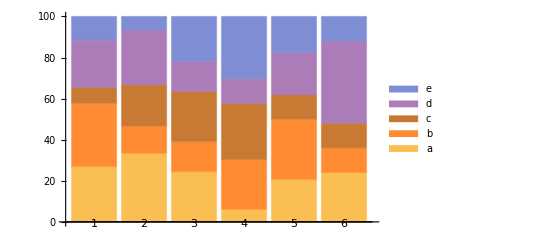

```mathematica
BarChart[data,ChartLayout->"Percentile",ChartLabels->{{"1","2","3","4","5","6"},None},
ChartLegends->{"a","b","c","d","e"}]
```

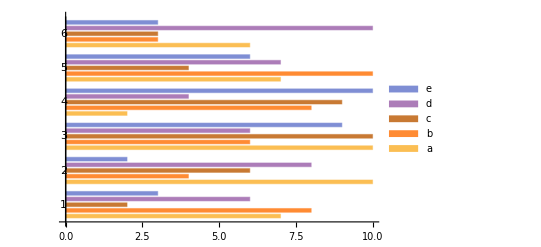

```mathematica
BarChart[data,ChartLabels->{{"1","2","3","4","5","6"},None},
ChartLegends->{"a","b","c","d","e"},
BarOrigin->Left]
```

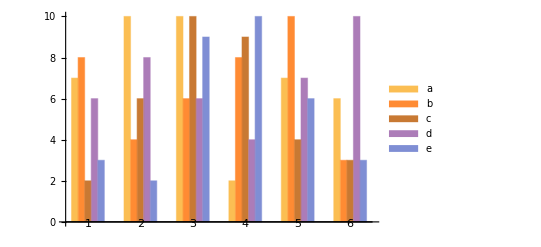

```mathematica
BarChart[data,ChartLabels->{{"1","2","3","4","5","6"},None},
ChartLegends->{"a","b","c","d","e"},
BarSpacing->{0,3}]
```

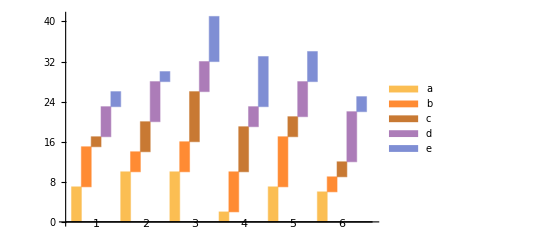

```mathematica
BarChart[data,ChartLabels->{{"1","2","3","4","5","6"},None},
ChartLegends->{"a","b","c","d","e"},
ChartLayout->"Stepped",
BarSpacing->{0,0}]
```

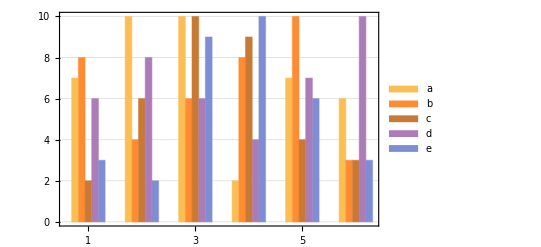

```mathematica
BarChart[data,ChartLabels->{{"1","2","3","4","5","6"},None},
ChartLegends->{"a","b","c","d","e"},
PlotTheme->"Detailed",
BarSpacing->{0,3}]
```

```mathematica
funcs={3/2 Sin[15x],Cos[x/2],x};
```

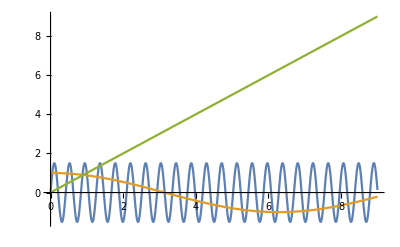

```mathematica
Plot[funcs,{x,0,9}]
```

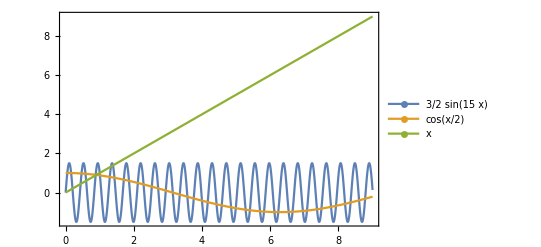

```mathematica
Plot[funcs,{x,0,9},Frame->True,PlotLegends->LineLegend[funcs,LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],Dividers->{{True,False,True},{True,True,False,False,True}}]&),LegendMarkers->"OpenMarkers"],Axes->False]
```

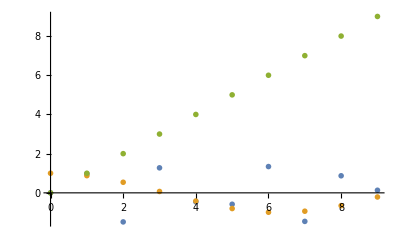

```mathematica
ListPlot[Table[funcs,{x,0,9,1}]//Transpose,PlotMarkers->"OpenMarkers",DataRange->{0,9}]
```

```mathematica
Plot[funcs,{x,0,9},
Frame->True,
Axes->False,
PlotLegends->LineLegend[
funcs,
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,False,True}}]&),
LegendMarkers->"OpenMarkers"]]
```

-Graphics-

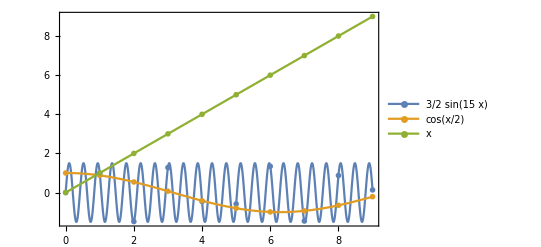

```mathematica
Show[Plot[funcs,{x,0,9},
Frame->True,Axes->False,
PlotLegends->LineLegend[
funcs,
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,False,True}}]&),
LegendMarkers->"OpenMarkers"]],ListPlot[Table[funcs,{x,0,9,1}]//Transpose,PlotMarkers->"OpenMarkers",DataRange->{0,9}]]
```

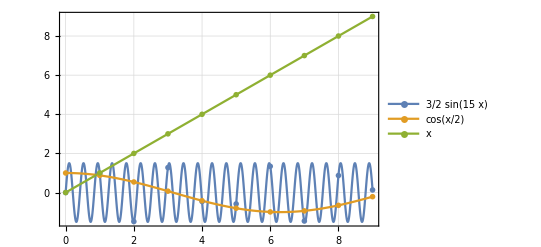

```mathematica
Show[Plot[funcs,{x,0,9},
PlotLegends->LineLegend[
funcs,
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,False,True}}]&),
LegendMarkers->"OpenMarkers"],PlotTheme->"Detailed"],ListPlot[Table[funcs,{x,0,9,1}]//Transpose,PlotMarkers->"OpenMarkers",DataRange->{0,9},PlotTheme->"Detailed"]]
```

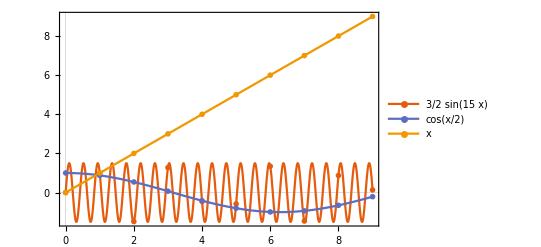

```mathematica
Show[Plot[funcs,{x,0,9},
PlotLegends->LineLegend[
funcs,
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,False,True}}]&),
LegendMarkers->"OpenMarkers"],PlotTheme->"Scientific"],ListPlot[Table[funcs,{x,0,9,1}]//Transpose,PlotMarkers->"OpenMarkers",DataRange->{0,9},PlotTheme->"Scientific"]]
```

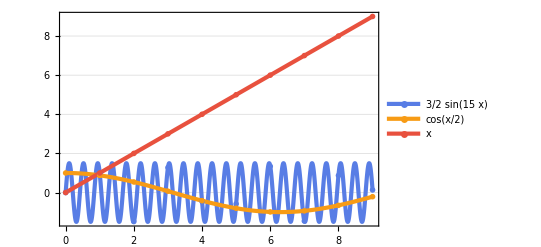
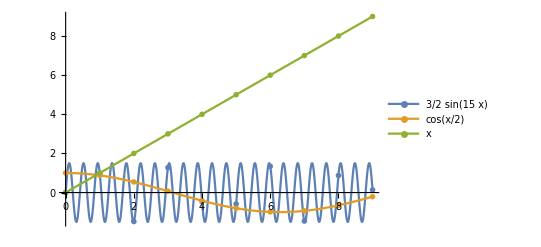
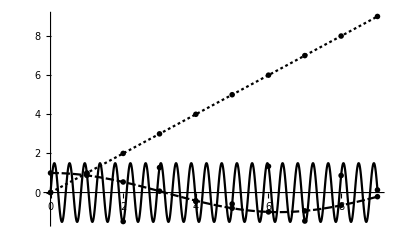
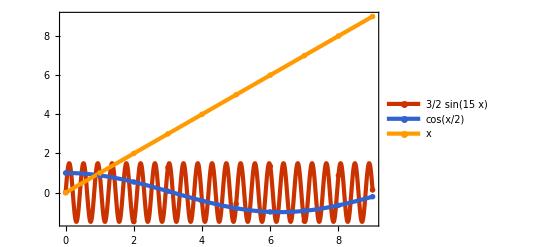
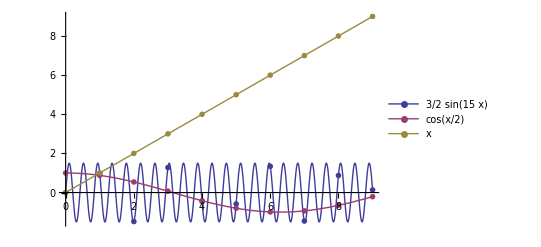
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[Plot[funcs,{x,0,9},
PlotLegends->LineLegend[
funcs,
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,False,True}}]&),
LegendMarkers->"OpenMarkers"],PlotTheme->#],ListPlot[Table[funcs,{x,0,9,1}]//Transpose,PlotMarkers->"OpenMarkers",DataRange->{0,9},PlotTheme->#]]&/@{"Business","Detailed","Marketing","Minimal","Monochrome","Scientific","Web","Classic"}
```

```mathematica
pdfs={PDF[NormalDistribution[-4,2],x],PDF[NormalDistribution[4,6],x],1/2 PDF[NormalDistribution[-3,1],x]+1/2 PDF[NormalDistribution[5,1.5],x]};
```

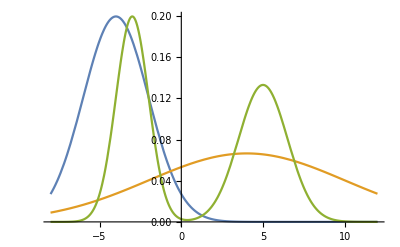

```mathematica
Plot[pdfs,{x,-8,12}]
```

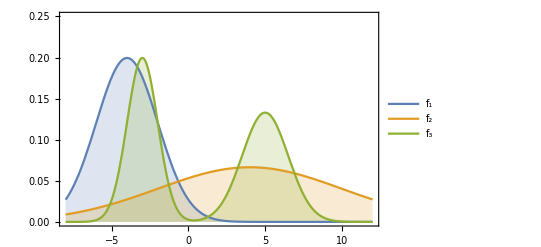

```mathematica
Plot[pdfs,{x,-8,12},Filling->Axis,PlotLegends->{"f_1","f_2","f_3"},Frame->True,Axes->False,PlotRange->{{-8,12},{0,0.25}}]
```

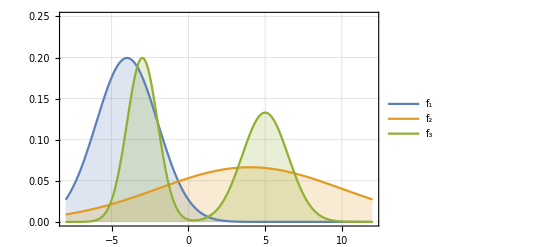

```mathematica
Plot[pdfs,{x,-8,12},Filling->Axis,PlotLegends->{"f_1","f_2","f_3"},PlotRange->{{-8,12},{0,0.25}},PlotTheme->"Detailed"]
```

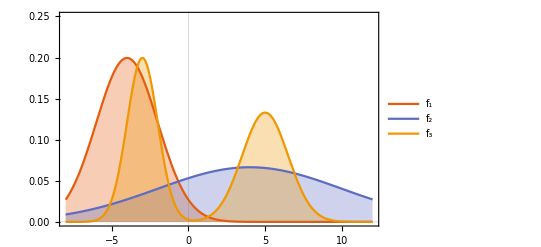

```mathematica
Plot[pdfs,{x,-8,12},Filling->Axis,PlotLegends->{"f_1","f_2","f_3"},PlotRange->{{-8,12},{0,0.25}},PlotTheme->"Scientific"]
```

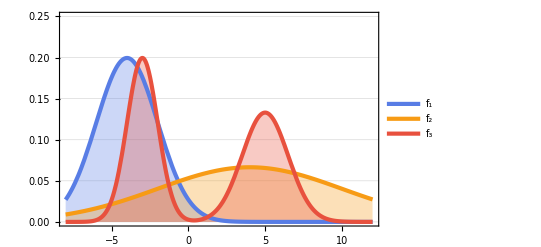
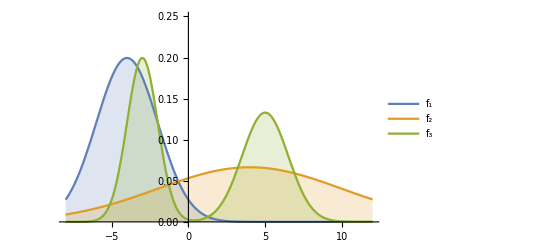
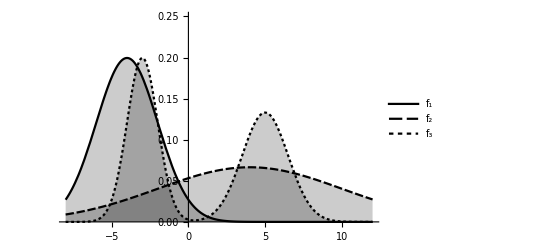
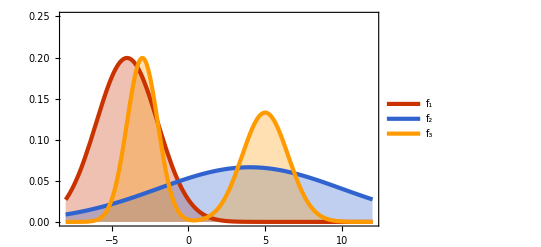
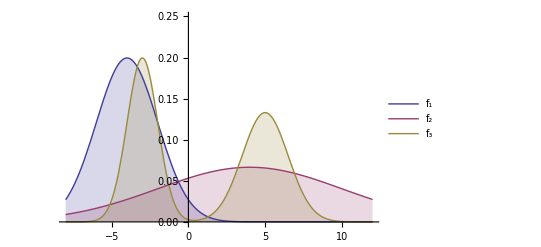
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[pdfs,{x,-8,12},Filling->Axis,PlotLegends->{"f_1","f_2","f_3"},PlotRange->{{-8,12},{0,0.25}},PlotTheme->#]&/@{"Business","Detailed","Marketing","Minimal","Monochrome","Scientific","Web","Classic"}
```